# Cuaderno de Prácticas

## Álgebra

## Grado en Ingeniería Informática

## CURSO 2025/26

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : A
Grupo de prácticas :1

## Grafos

```mathematica
(* Cap 5 - 2.2. Matriz de adyacencia - Función 5.1 *)
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
(* Cap 5 - 2.2. Matriz de adyacencia - Función 5.2 *)
MATRIZADYACENCIADIR[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1,{k,Length[F]}];
matrizadyacencia];
(* Cap 5 - 4 Grafos Isomorfos - Función 5.10 *)
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],   
matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];   
Do[	      
If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
Print["Son isomorfos, una matriz P es: ",MatrixForm[matrizP], 
      ", una permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
(* Conexo *)
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]
```

```mathematica
(* Cap 5 - 2.2. Matriz de incidencia - Función 5.5 *)
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j,nuevoF,CONTADORi},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizincidencia=Table[0,{i,Length[W]},{j,Length[F]}];
Do[Do[
matrizincidencia[[nuevoF[[j]][[i]],j]]=1;
,{i,2}];,{j,Length[F]}];
matrizincidencia
];
(* NColoraciones *)
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
(* NumeroCromatico *)
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
(* D3 *)
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]
(* QuitarVerticesGrado210 *)
QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]
(**)
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
(**)
EULER[matrizadyacencia_]:=Module[{A,i},
   Euler=True;
   If[CONEXO[matrizadyacencia],
      A=matrizadyacencia.matrizadyacencia;
      Do[
         If[Mod[A[[i,i]],2]==1,Euler=False;Break[];];
      ,{i,Length[matrizadyacencia]}];
   ,
      Euler=False;
   ];
   Euler
]
(**)
HAMILTON[A_]:=Module[{ciclos,adyacentes,ultvertice,ciclostemp,k,t,j,i},
ciclos={{1}};
Do[
ciclostemp={};
Do[
adyacentes={};

ultvertice=ciclos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,ciclos[[k]]];
If[adyacentes≠{},

Do[AppendTo[ciclostemp,Append[ciclos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[ciclos]}];
ciclos=ciclostemp;
,{i,Dimensions[A][[1]]-1}];
ciclostemp={};
Do[If[A[[1,ciclos[[k]][[Dimensions[A][[1]]]]]]==1,AppendTo[ciclostemp,Append[ciclos[[k]],1]];];,{k,Length[ciclos]}];
ciclostemp
];
(**)
CAMINOS[vertice1_,vertice2_,longitud_,matrizadyacencia_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[matrizadyacencia[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[matrizadyacencia][[1]]}];


If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud}];
caminostemp={};
Do[If[caminos[[k]][[longitud+1]]==vertice2,AppendTo[caminostemp,caminos[[k]]];];,{k,Length[caminos]}];
caminostemp
];
(**)
distancia[u_,v_,matrizadyacencia_]:=Module[{B},
n=1;
B=matrizadyacencia;
While[B[[u,v]]==0 && n<Dimensions[B][[1]],n++;B=MatrixPower[matrizadyacencia,n];];
If[n==Dimensions[B][[1]],Print["No están conectados"];,
Print[B[[u,v]]," geodésica/s. Distancia: ",n];];
]
(**)
GEODESICAS[u_,v_,matrizadyacencia_]:=Module[{B},
n=1;
B=matrizadyacencia;
While[B[[u,v]]==0 && n<Dimensions[B][[1]],n++;B=MatrixPower[matrizadyacencia,n];];
If[n==Dimensions[B][[1]],Print["No están conectados"];,
Print[CAMINOS[u,v,n,matrizadyacencia]]];
]
(**)
```

```mathematica
<<"Combinatorica`";
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

SetDelayed::write: Tag TreeQ in TreeQ[g_Graph] is Protected.

```mathematica
IND[W1_,F_]:=Module[{i},
F1={};
Do[If[Sort[Intersection[{F[[i]][[1]],F[[i]][[2]]},W1]]==Sort[{F[[i]][[1]],F[[i]][[2]]}],AppendTo[F1,F[[i]]]],{i,Length[F]}];
F1
]
(* Sesión 5 cap 6 *)
BIPARTITO[W_,F_]:=Module[{i,subconjuntos,j,fin},
bipartito=False;
i=1;
fin=Quotient[Length[W],2];
While[!bipartito && i<=fin,
subconjuntos=KSubsets[W,i];
j=1;
While[!bipartito && j<=Length[subconjuntos],
If[IND[subconjuntos[[j]],F]=={},
If[IND[Complement[W,subconjuntos[[j]]],F]=={},
bipartito=True;
W1=subconjuntos[[j]];
W2=Complement[W,subconjuntos[[j]]];
];
];
j++;];
i++;];
If[bipartito,Print["Es bipartito: W1=",W1," y W2=",W2];
If[Length[F]==Length[W1]*Length[W2],Print["Es bipartito completo: ",Subscript["K", Length[W1],Length[W2]]  ], Print["No es bipartito completo"]];
,Print["No es bipartito"]];
]
(* Sesión 5 cap 6 *)
REGULAR[matrizadyacencia_]:=Module[{i,j},
grado=Sum[matrizadyacencia[[1,j]],{j,Dimensions[matrizadyacencia][[1]]}];
regular=True;
Do[
If[grado!=Sum[matrizadyacencia[[i,j]],{j,1,Dimensions[matrizadyacencia][[1]]}],regular=False;Break[];];
,{i,2,Dimensions[matrizadyacencia][[1]]}];
regular
];
(* Sesión 5 cap 6 *)
COMPLETO[matrizadyacencia_]:=   (Sum[MatrixPower[matrizadyacencia,2][[i,i]],{i,Dimensions[matrizadyacencia][[1]]}]==Dimensions[matrizadyacencia][[1]]*(Dimensions[matrizadyacencia][[1]]-1))
(* K33 *)
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]
(* HomeoMorfoK5K33 *)
HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]
(* Plano *)
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
(* Arbol *)
ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
arbol=False;
If[CONEXO[matrizadyacencia],
arbol=(Dimensions[matrizadyacencia][[1]]==(Sum[matrizadyacencia[[i,j]],{i,Dimensions[matrizadyacencia][[1]]},{j,Dimensions[matrizadyacencia][[2]]}]/2)+1);
];
arbol
]
(* Dibujar *)
(**)
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

## Práctica 4

### Ejercicio 5.29 a) Sea W el conjunto formado por todas las cifras distintas que componen su DNI junto con todas las letras distintas de su primer apellido. b) Consideramos el grafo no orientado G₁ cuyo conjunto de vértices es W y donde dos vértices cualesquiera serán adyacentes si y sólo si son: I. Un número par y una vocal. II. Un número impar y una consonante. III. Dos números pares distintos. c) Consideramos el grafo dirigido G₂ cuyo conjunto de vértices es W y donde el conjunto de flechas está formado por todas aquellas flechas que podemos considerar de la forma: I. Origen en un número impar y fin en una vocal. II. Origen en una vocal y fin en una consonante. III. Origen en un número par y fin en un número impar. Se pide:

#### I) Definir G₁ y G₂ directamente por sus conjuntos de vértices y lados o flechas.

```mathematica
W={2,6,8,0,"n","m","a","r","t","i","l","u","s"};
F1={
	{2,"a"},{2,"i"},{2,"u"},{6,"a"},{6,"i"},{6,"u"},{8,"a"},{8,"i"},{8,"u"},
	{0,"n"},{0,"m"},{0,"r"},{0,"t"},{0,"l"},{0,"s"},
	{2,6},{2,8},{6,8}
};
F2={
	{0,"a"},{0,"i"},{0,"u"},
	{"a","n"},{"a","m"},{"a","r"},{"a","t"},{"a","l"},{"a","s"},
	{"i","n"},{"i","m"},{"i","r"},{"i","t"},{"i","l"},{"i","s"},
	{"u","n"},{"u","m"},{"u","r"},{"u","t"},{"u","l"},{"u","s"},
	{2,0},{6,0},{8,0}
};
```

#### II) Calcular las matrices de adyacencia de G₁ y G₂.

```mathematica
Eje529G1Adya=MATRIZADYACENCIA[W,F1];
Eje529G1Adya//MatrixForm
```

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eje529G2Adya=MATRIZADYACENCIADIR[W,F2];
Eje529G2Adya//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### III) Calcular la matriz de incidencia de G₁.

```mathematica
M1=MATRIZINCIDENCIA[W,F1];
M1//MatrixForm
```

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

#### IV) Representar gráficamente G₁ y G₂.

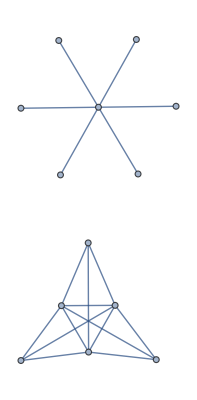

```mathematica
GraphPlot[Eje529G1Adya]
```

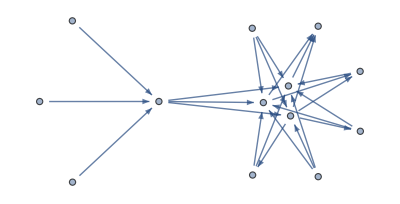

```mathematica
GraphPlot[Eje529G2Adya,EdgeRenderingFunction->({Arrow[#1,0.1]}&)]
```

### Ejercicio 2 Calcular conjunto de vértices y lados, matriz de adyacencia, matriz de incidencia y representación gráfica de los grafos del ejercicio 6.8 del manual de prácticas

#### a) -Graphics-

```mathematica
WEjer2GIa={1,2,3,4,5,6};
FEjer2GIa={1->2,3->1,4->5,6->1}

"MATRIZADYACENCIA"
Eje68G1Adya=MATRIZADYACENCIA[WEjer2GIa,FEjer2GIa];
Eje68G1Adya//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIa=MATRIZINCIDENCIA[WEjer2GIa,FEjer2GIa];
IEjer2GIa//MatrixForm
"Vertices y lados"
matrizadyacencia=Eje68G1Adya;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];
	,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[
					matrizadyacencia][[1]]}];
F
"Representacion gráfica"
GraphPlot[Eje68G1Adya,DirectedEdges->True]
```

{1→2,3→1,4→5,6→1}

MATRIZADYACENCIA

(0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

MATRIZINCIDENCIA

(1 | 1 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Vertices y lados

{1,2,3,4,5,6}

{2→1,3→1,6→1,1→2,1→3,5→4,4→5,1→6}

Representacion gráfica

-Graphics-

#### b)-Graphics-

```mathematica
Eje68G2Adya=({{0, 1, 0, 1}, {1, 0, 1, 0}, {0, 1, 0, 1}, {1, 0, 1, 0}});
Wb=Table[i,{i,Dimensions[Eje68G2Adya]⟦1⟧}]
Fb={};
Do[Do[If[Eje68G2Adya⟦i,j⟧==1,AppendTo[Fb,i->j]];,{i,j}];
,{j,Dimensions[Eje68G2Adya]⟦1⟧}];
Fb
```

{1,2,3,4}

{1→2,2→3,1→4,3→4}

MATRIZINCIDENCIA

(1 | 0 | 1 | 0
1 | 1 | 0 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 1)

Vertices y lados

{1,2,3,4}

{2→1,4→1,2→1,4→1}

Representacion gráfica

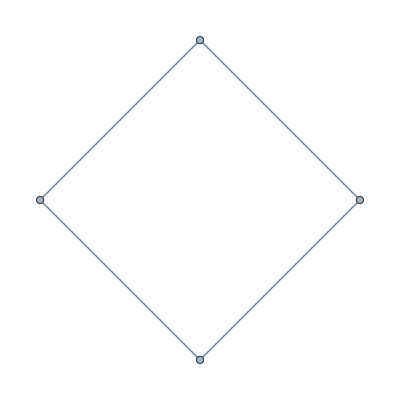

```mathematica
WEjer2GIb={1,2,3,4};
FEjer2GIb={1->2,2->3,1->4,3->4};
"MATRIZINCIDENCIA"
IEjer2GIb=MATRIZINCIDENCIA[WEjer2GIb,FEjer2GIb];
IEjer2GIb//MatrixForm
"Vertices y lados"
W=Table[i,{i,Dimensions[Eje68G2Adya][[1]]}]
F={};
Do[Do[If[Eje68G2Adya[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[
								Eje68G2Adya][[1]]}];,{j,Eje68G2Adya[[1]]}];
F
"Representacion gráfica"
GraphPlot[Eje68G2Adya]
```

#### c)-Graphics-

```mathematica
matrizincidenciaEjer2GIc=({{1, 1, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 1, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}});

W=Table[i,{i,Dimensions[matrizincidenciaEjer2GIc][[1]]}]
F={};
Do[
AppendTo[F,Position[Transpose[matrizincidenciaEjer2GIc]
[[i]],1][[1]][[1]]->Position[Transpose[matrizincidenciaEjer2GIc][[i]],1][[2]][[1]]]
,{i,Dimensions[matrizincidenciaEjer2GIc][[2]]}];
F
```

{1,2,3,4,5}

{1→4,1→5,2→4,2→5,3→4,3→5}

MATRIZADYACENCIA

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

Vertices y lados

{1,2,3,4,5}

{4→1,5→1,4→2,5→2,4→3,5→3,1→4,2→4,3→4,1→5,2→5,3→5}

Representacion gráfica

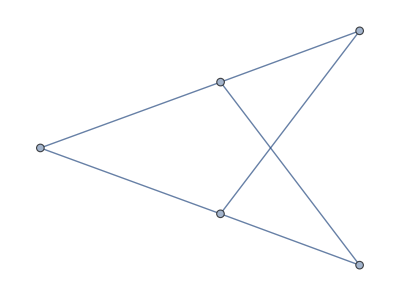

```mathematica
WEjer2GIc={1,2,3,4,5};
FEjer2GIc={1->4,1->5,2->4,2->5,3->4,3->5};
"MATRIZADYACENCIA"
Eje68G3Adya=MATRIZADYACENCIA[WEjer2GIc,FEjer2GIc];
Eje68G3Adya//MatrixForm
"Vertices y lados"
W=Table[i,{i,Dimensions[Eje68G3Adya][[1]]}]
F={};
Do[Do[If[Eje68G3Adya[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[
					Eje68G3Adya][[1]]}];,{j,Dimensions[Eje68G3Adya][[1]]}];
F
"Representacion gráfica"
GraphPlot[Eje68G3Adya]
```

#### d)-Graphics-

d

MATRIZADYACENCIA

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

MATRIZINCIDENCIA

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1)

Vertices y lados

{1,2,3,4,5,6,7,8}

{2→1,4→1,8→1,1→2,3→2,7→2,2→3,4→3,6→3,1→4,3→4,5→4,4→5,6→5,8→5,3→6,5→6,7→6,2→7,6→7,8→7,1→8,5→8,7→8}

Representacion gráfica

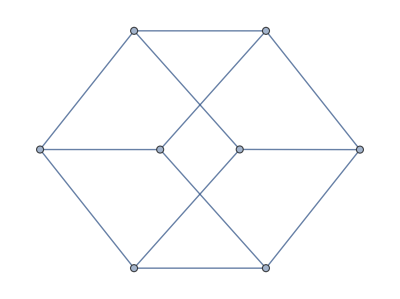

```mathematica
"d"
WEjer2GIdg4={1,2,3,4,5,6,7,8};
FEjer2GIdg4={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1,1->4,2->7,3->6,5->8};
"MATRIZADYACENCIA"
Eje68G4Adya=MATRIZADYACENCIA[WEjer2GIdg4,FEjer2GIdg4];
Eje68G4Adya//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIdg4=MATRIZINCIDENCIA[WEjer2GIdg4,FEjer2GIdg4];
IEjer2GIdg4//MatrixForm
"Vertices y lados"
matrizadyacencia=Eje68G4Adya;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[
			matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
"Representacion gráfica"
GraphPlot[Eje68G4Adya]
```

MATRIZADYACENCIA

(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)

MATRIZINCIDENCIA

(1 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1)

Vertices y lados

{1,2,3,4}

{2→1,3→1,4→1,1→2,3→2,4→2,1→3,2→3,4→3,1→4,2→4,3→4}

Representacion gráfica

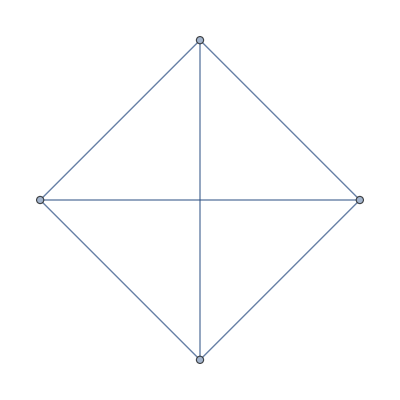

```mathematica
WEjer2GIdg5={1,2,3,4};
FEjer2GIdg5={{1,2},{2,3},{3,1},{1,4},{2,4},{3,4}};
"MATRIZADYACENCIA"
Eje68G5Adya=MATRIZADYACENCIA[WEjer2GIdg5,FEjer2GIdg5];
Eje68G5Adya//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIdg5=MATRIZINCIDENCIA[WEjer2GIdg5,FEjer2GIdg5];
IEjer2GIdg5//MatrixForm
"Vertices y lados"
matrizadyacencia=Eje68G5Adya;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[
			matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
"Representacion gráfica"
GraphPlot[Eje68G5Adya]
```

### Ejercicio 3 Ejercicio 5.4 del manual de prácticas Estudiar si son isomorfos los siguientes grafos

#### a) -Graphics-

```mathematica
WEjer3GIdgb={1,2,3,4,5,6};
FEjer3GIdgb={{1,2},{2,3},{3,6},{6,5},{5,4},{4,1}};
Eje54G1Adya=MATRIZADYACENCIA[WEjer3GIdgb,FEjer3GIdgb];
MatrixForm[Eje54G1Adya]
```

(0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0)

#### b) -Graphics-

```mathematica
Eje54G2Adya=({{0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0}});
MatrixForm[Eje54G2Adya]
```

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0)

#### c) -Graphics-

```mathematica
WEjer3GIdgc={1,2,3,4,5,6};
FEjer3GIdgc={{1,6},{1,5},{2,4},{2,6},{3,4},{3,5}};
Eje54G3Adya=MATRIZADYACENCIA[WEjer3GIdgc,FEjer3GIdgc];
MatrixForm[Eje54G3Adya]
```

(0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0)

#### d) -Graphics-

```mathematica
Eje54G4Adya=({{0, 1, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1}, {0, 0, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1}, {1, 1, 0, 0, 1, 0}});
MatrixForm[Eje54G4Adya]
```

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1 | 0)

#### e) -Graphics-

```mathematica
matrizincidenciaEjer3GIe=({{1, 0, 0, 1, 0, 0}, {0, 1, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 1, 0, 0, 1}, {0, 1, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 1}});


W=Table[i,{i,Dimensions[matrizincidenciaEjer3GIe][[1]]}]
F={};
Do[
AppendTo[F,Position[Transpose[matrizincidenciaEjer3GIe][[i]],1][[1]][[1]]->Position[Transpose[matrizincidenciaEjer3GIe][[i]],1][[2]][[1]]]
,{i,Dimensions[matrizincidenciaEjer3GIe][[2]]}];
F
```

{1,2,3,4,5,6}

{1→6,2→5,3→4,1→2,3→5,4→6}

```mathematica
WEjer3GIdge={1,2,3,4,5,6};
FEjer3GIdge={1->6,2->5,3->4,1->2,3->5,4->6};
Eje54G5Adya=MATRIZADYACENCIA[WEjer3GIdge,FEjer3GIdge];
MatrixForm[Eje54G5Adya]
```

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0)

#### f) -Graphics-

```mathematica
WEjer3GIdgf={1,2,3,4,5,6};
FEjer3GIdgf={1->2, 1->3, 2->3, 3->5, 4->5,4->6, 5->6};
Eje54G6Adya=MATRIZADYACENCIA[WEjer3GIdgf,FEjer3GIdgf];
MatrixForm[Eje54G6Adya]
```

(0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0)

```mathematica
"Ga y Gb"
ISOMORFOS[Eje54G1Adya,Eje54G2Adya]
"Ga y Gc"
ISOMORFOS[Eje54G1Adya,Eje54G3Adya]
"Ga y Gd"
ISOMORFOS[Eje54G1Adya,Eje54G4Adya]
"Ga y Ge"
ISOMORFOS[Eje54G1Adya,Eje54G5Adya]
"Ga y Gf"
ISOMORFOS[Eje54G1Adya,Eje54G6Adya]
"Gb y Gc"
ISOMORFOS[Eje54G2Adya,Eje54G3Adya]
"Gb y Gd"
ISOMORFOS[Eje54G2Adya,Eje54G4Adya]
"Gb y Ge"
ISOMORFOS[Eje54G2Adya,Eje54G5Adya]
"Gb y Gf"
ISOMORFOS[Eje54G2Adya,Eje54G6Adya]
"Gc y Gd"
ISOMORFOS[Eje54G3Adya,Eje54G4Adya]
"Gc y Ge"
ISOMORFOS[Eje54G3Adya,Eje54G5Adya]
"Gc y Gf"
ISOMORFOS[Eje54G3Adya,Eje54G6Adya]
"Gd y Ge"
ISOMORFOS[Eje54G4Adya,Eje54G5Adya]
"Gd y Gf"
ISOMORFOS[Eje54G4Adya,Eje54G6Adya]
"Ge y Gf"
ISOMORFOS[Eje54G5Adya,Eje54G6Adya]
```

Ga y Gb

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 3 | 6 | 5 | 4)

Ga y Gc

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 3 | 5 | 6 | 4 | 2)

Ga y Gd

No son isomorfos

Ga y Ge

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 6 | 5 | 3 | 4)

Ga y Gf

No son isomorfos

Gb y Gc

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 3 | 5 | 4 | 6 | 2)

Gb y Gd

No son isomorfos

Gb y Ge

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 4 | 5 | 3 | 6)

Gb y Gf

No son isomorfos

Gc y Gd

No son isomorfos

Gc y Ge

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 5 | 4 | 2 | 3 | 6)

Gc y Gf

No son isomorfos

Gd y Ge

No son isomorfos

Gd y Gf

No son isomorfos

Ge y Gf

No son isomorfos

## Práctica 5

### Ejercicio 2 Calcular conjunto de vértices y lados, matriz de adyacencia, matriz de incidencia y representación gráfica de los grafos del ejercicio 6.8 del manual de prácticas

#### a) -Graphics-

```mathematica
"¿Es completo?"
COMPLETO[Eje68G1Adya]
"¿Es regular?"
REGULAR[Eje68G1Adya]
"¿Es bipartito?"
BIPARTITO[WEjer2GIa,FEjer2GIa]
```

¿Es completo?

False

¿Es regular?

False

¿Es bipartito?

Es bipartito: W1={1,4} y W2={2,3,5,6}

No es bipartito completo

#### b)-Graphics-

```mathematica
"¿Es completo?"
COMPLETO[Eje68G2Adya]
"¿Es regular?"
REGULAR[Eje68G2Adya]
"¿Es bipartito?"
BIPARTITO[WEjer2GIb,FEjer2GIb]
```

¿Es completo?

False

¿Es regular?

True

¿Es bipartito?

Es bipartito: W1={1,3} y W2={2,4}

Es bipartito completo: K_(2,2)

#### c)-Graphics-

```mathematica
"¿Es completo?"
COMPLETO[Eje68G3Adya]
"¿Es regular?"
REGULAR[Eje68G3Adya]
"¿Es bipartito?"
BIPARTITO[WEjer2GIc,FEjer2GIc]
```

¿Es completo?

False

¿Es regular?

False

¿Es bipartito?

Es bipartito: W1={4,5} y W2={1,2,3}

Es bipartito completo: K_(2,3)

#### d)-Graphics-

```mathematica
"d"
"¿Es completo?"
COMPLETO[Eje68G4Adya]
"¿Es regular?"
REGULAR[Eje68G4Adya]
"¿Es bipartito?"
BIPARTITO[WEjer2GIdg4,FEjer2GIdg4]
```

d

¿Es completo?

False

¿Es regular?

True

¿Es bipartito?

Es bipartito: W1={1,3,5,7} y W2={2,4,6,8}

No es bipartito completo

```mathematica
"¿Es completo?"
COMPLETO[Eje68G5Adya]
"¿Es regular?"
REGULAR[Eje68G5Adya]
"¿Es bipartito?"
BIPARTITO[WEjer2GIdg5,FEjer2GIdg5]
```

¿Es completo?

True

¿Es regular?

True

¿Es bipartito?

No es bipartito

### Ejercicio 2 Estudiar si el grafo del ejercicio 3 de la convocatoria ordinaria 2 del curso 2023/24, es regular, completo, bipartito y/o bipartito completo. Análogamente para in octógono K6 y K4,3.

```mathematica
WEjerGIdg1={1,2,3,4,5,6};
FEjerGIdg1={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{1,4},{2,5},{3,6}};
"MATRIZADYACENCIA"
Eje3Ord22324Adya=MATRIZADYACENCIA[WEjerGIdg1,FEjerGIdg1];
Eje3Ord22324Adya//MatrixForm
"¿Es completo?"
COMPLETO[Eje3Ord22324Adya]
"¿Es regular?"
REGULAR[Eje3Ord22324Adya]
"¿Es bipartito?"
BIPARTITO[WEjerGIdg1,FEjerGIdg1]
```

MATRIZADYACENCIA

(0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0)

¿Es completo?

False

¿Es regular?

True

¿Es bipartito?

Es bipartito: W1={1,3,5} y W2={2,4,6}

Es bipartito completo: K_(3,3)

#### Octogono

```mathematica
octoW={1,2,3,4,5,6,7,8};
octoF={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,1}};
octoAdya=({{0, 1, 0, 0, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 0, 0, 1, 0}});
"¿Es completo?"
COMPLETO[octoAdya]
"¿Es regular?"
REGULAR[octoAdya]
"¿Es bipartito?"
BIPARTITO[octoW,octoF]
```

¿Es completo?

False

¿Es regular?

True

¿Es bipartito?

Es bipartito: W1={1,3,5,7} y W2={2,4,6,8}

No es bipartito completo

#### K6

MATRIZADYACENCIA

(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 0)

¿Es completo?

True

¿Es regular?

True

¿Es bipartito?

No es bipartito

Representacion gráfica

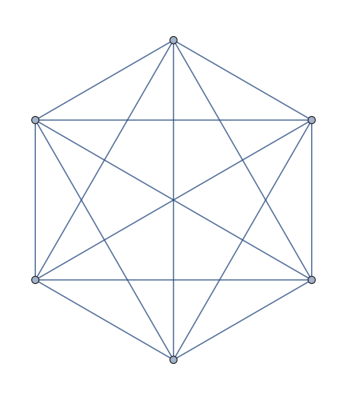

```mathematica
WEjerGIdg3=Range[6];
FEjerGIdg3=Subsets[WEjerGIdg3, {2}];
"MATRIZADYACENCIA"
AEjerGIdg3=MATRIZADYACENCIA[WEjerGIdg3,FEjerGIdg3];
AEjerGIdg3//MatrixForm
"¿Es completo?"
COMPLETO[AEjerGIdg3]
"¿Es regular?"
REGULAR[AEjerGIdg3]
"¿Es bipartito?"
BIPARTITO[WEjerGIdg3,FEjerGIdg3]
"Representacion gráfica"
GraphPlot[AEjerGIdg3]
```

#### K4,3

(0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0)

¿Es completo?

False

¿Es regular?

False

¿Es bipartito?

Es bipartito: W1={5,6,7} y W2={1,2,3,4}

Es bipartito completo: K_(3,4)

Representacion gráfica

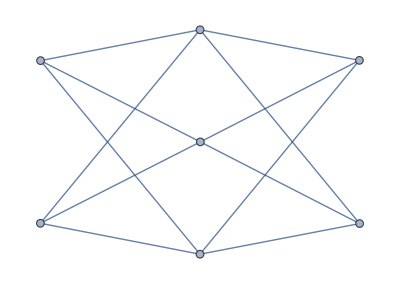

```mathematica
WEjerGIdg4 = {1,2,3,4,5,6,7};
A = {1,2,3,4};
B = {5,6,7};
FEjerGIdg4 = Flatten[
   Table[{i,j}, {i,A}, {j,B}],
   1
];
"MATRIZ ADYACENCIA";
k43Adya = MATRIZADYACENCIA[WEjerGIdg4, FEjerGIdg4];
k43Adya // MatrixForm
"¿Es completo?"
COMPLETO[k43Adya]
"¿Es regular?"
REGULAR[k43Adya]
"¿Es bipartito?"
BIPARTITO[WEjerGIdg4, FEjerGIdg4]
"Representacion gráfica"
GraphPlot[k43Adya]
```

## Práctica 6

### Ejercicio 1 Se pide: i. Comprobar si es conexo ii. Calcular sus componentes conexas iii. Comprobar si es de Euler iv. Comprobar si es Hamilton v. Utilizar el teorema del número de caminos para calcular la distancia entre el primer y último vértice de cada grafo vi. Determinar, si existen un ciclo de Euler, un ciclo de Hamilton y una geodésica entre el primer y el último vértice del grafo. Dados los siguientes grafos

#### a) Cada uno de los grafos del ejercicio 5.29 del manual de prácticas

```mathematica
"---------------"
"Ejercicio 5.39 G1"
"---------------"
Clear[pract6Adya]
pract6Adya=Eje529G1Adya;
(* Primer y último vértice *)
u = 1;
v = Length[pract6Adya];

Print["Matriz de adyacencia:"];
Print[MatrixForm[pract6Adya]];

(* i) Comprobar si es conexo *)
Print["i) ¿Es conexo?"];
esConexo = CONEXO[pract6Adya];
Print[esConexo];

(* ii) Componentes conexas *)
Print["ii) Componentes conexas:"];
componentes = COMPONENTESCONEXAS[pract6Adya];
Print[componentes];

(* iii) Comprobar si es de Euler *)
Print["iii) ¿Es de Euler?"];
esEuler = EULER[pract6Adya];
Print[esEuler];

(* iv) Comprobar si es Hamilton *)
Print["iv) ¿Es Hamilton?"];
ciclosHamilton = HAMILTON[pract6Adya];
esHamilton = ciclosHamilton =!= {};
Print[esHamilton];

(* v) Distancia entre el primer y el último vértice *)
Print["v) Distancia entre el primer y el último vértice:"];
dist = distancia[u, v, pract6Adya];
Print["Distancia entre ", u, " y ", v, " = ", dist];

(* También puedes comprobar el teorema del número de caminos *)
Print["Caminos de longitud 1 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 1, pract6Adya]];

Print["Caminos de longitud 2 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 2, pract6Adya]];

Print["Caminos de longitud 3 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 3, pract6Adya]];

(* vi) Determinar si existen ciclo de Euler, ciclo de Hamilton y geodésica *)
Print["vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica"];

If[esEuler,
   Print["Sí existe ciclo de Euler."],
   Print["No existe ciclo de Euler."]
];

If[esHamilton,
   Print["Sí existe ciclo de Hamilton."];
   Print["Un ciclo de Hamilton es: ", First[ciclosHamilton]],
   Print["No existe ciclo de Hamilton."]
];

geodesicas = GEODESICAS[u, v, pract6Adya];
If[geodesicas =!= {},
   Print["Sí existe geodésica entre ", u, " y ", v, "."];
   Print["Geodésicas: ", geodesicas],
   Print["No existe geodésica entre ", u, " y ", v, "."]
];
"---------------"
"Ejercicio 5.39 G2"
"---------------"
Clear[pract6Adya]
pract6Adya=Eje529G2Adya;
(* Primer y último vértice *)
u = 1;
v = Length[pract6Adya];

Print["Matriz de adyacencia:"];
Print[MatrixForm[pract6Adya]];

(* i) Comprobar si es conexo *)
Print["i) ¿Es conexo?"];
esConexo = CONEXO[pract6Adya];
Print[esConexo];

(* ii) Componentes conexas *)
Print["ii) Componentes conexas:"];
componentes = COMPONENTESCONEXAS[pract6Adya];
Print[componentes];

(* iii) Comprobar si es de Euler *)
Print["iii) ¿Es de Euler?"];
esEuler = EULER[pract6Adya];
Print[esEuler];

(* iv) Comprobar si es Hamilton *)
Print["iv) ¿Es Hamilton?"];
ciclosHamilton = HAMILTON[pract6Adya];
esHamilton = ciclosHamilton =!= {};
Print[esHamilton];

(* v) Distancia entre el primer y el último vértice *)
Print["v) Distancia entre el primer y el último vértice:"];
dist = distancia[u, v, pract6Adya];
Print["Distancia entre ", u, " y ", v, " = ", dist];

(* También puedes comprobar el teorema del número de caminos *)
Print["Caminos de longitud 1 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 1, pract6Adya]];

Print["Caminos de longitud 2 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 2, pract6Adya]];

Print["Caminos de longitud 3 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 3, pract6Adya]];

(* vi) Determinar si existen ciclo de Euler, ciclo de Hamilton y geodésica *)
Print["vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica"];

If[esEuler,
   Print["Sí existe ciclo de Euler."],
   Print["No existe ciclo de Euler."]
];

If[esHamilton,
   Print["Sí existe ciclo de Hamilton."];
   Print["Un ciclo de Hamilton es: ", First[ciclosHamilton]],
   Print["No existe ciclo de Hamilton."]
];

geodesicas = GEODESICAS[u, v, pract6Adya];
If[geodesicas =!= {},
   Print["Sí existe geodésica entre ", u, " y ", v, "."];
   Print["Geodésicas: ", geodesicas],
   Print["No existe geodésica entre ", u, " y ", v, "."]
];
```

---------------

Ejercicio 5.39 G1

---------------

Matriz de adyacencia:

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

i) ¿Es conexo?

False

ii) Componentes conexas:

{{1,2,3,7,10,12},{4,5,6,8,9,11,13}}

iii) ¿Es de Euler?

False

iv) ¿Es Hamilton?

False

v) Distancia entre el primer y el último vértice:

No están conectados

Distancia entre 1 y 13 = Null

Caminos de longitud 1 entre 1 y 13:

{}

Caminos de longitud 2 entre 1 y 13:

{}

Caminos de longitud 3 entre 1 y 13:

{}

vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica

No existe ciclo de Euler.

No existe ciclo de Hamilton.

No están conectados

Sí existe geodésica entre 1 y 13.

Geodésicas: Null

---------------

Ejercicio 5.39 G2

---------------

Matriz de adyacencia:

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

i) ¿Es conexo?

False

ii) Componentes conexas:

{{1,4,5,6,7,8,9,10,11,12,13},{2},{3}}

iii) ¿Es de Euler?

False

iv) ¿Es Hamilton?

False

v) Distancia entre el primer y el último vértice:

3 geodésica/s. Distancia: 3

Distancia entre 1 y 13 = Null

Caminos de longitud 1 entre 1 y 13:

{}

Caminos de longitud 2 entre 1 y 13:

{}

Caminos de longitud 3 entre 1 y 13:

{{1,4,7,13},{1,4,10,13},{1,4,12,13}}

vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica

No existe ciclo de Euler.

No existe ciclo de Hamilton.

{{1,4,7,13},{1,4,10,13},{1,4,12,13}}

Sí existe geodésica entre 1 y 13.

Geodésicas: Null

#### b) Cada uno de los grafos del ejercicio 6.8 del manual de prácticas

```mathematica
"---------------"
"Ejercicio 6.8 G1"
"---------------"
Clear[pract6Adya]
pract6Adya=Eje68G1Adya;
(* Primer y último vértice *)
u = 1;
v = Length[pract6Adya];

Print["Matriz de adyacencia:"];
Print[MatrixForm[pract6Adya]];

(* i) Comprobar si es conexo *)
Print["i) ¿Es conexo?"];
esConexo = CONEXO[pract6Adya];
Print[esConexo];

(* ii) Componentes conexas *)
Print["ii) Componentes conexas:"];
componentes = COMPONENTESCONEXAS[pract6Adya];
Print[componentes];

(* iii) Comprobar si es de Euler *)
Print["iii) ¿Es de Euler?"];
esEuler = EULER[pract6Adya];
Print[esEuler];

(* iv) Comprobar si es Hamilton *)
Print["iv) ¿Es Hamilton?"];
ciclosHamilton = HAMILTON[pract6Adya];
esHamilton = ciclosHamilton =!= {};
Print[esHamilton];

(* v) Distancia entre el primer y el último vértice *)
Print["v) Distancia entre el primer y el último vértice:"];
dist = distancia[u, v, pract6Adya];
Print["Distancia entre ", u, " y ", v, " = ", dist];

(* También puedes comprobar el teorema del número de caminos *)
Print["Caminos de longitud 1 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 1, pract6Adya]];

Print["Caminos de longitud 2 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 2, pract6Adya]];

Print["Caminos de longitud 3 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 3, pract6Adya]];

(* vi) Determinar si existen ciclo de Euler, ciclo de Hamilton y geodésica *)
Print["vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica"];

If[esEuler,
   Print["Sí existe ciclo de Euler."],
   Print["No existe ciclo de Euler."]
];

If[esHamilton,
   Print["Sí existe ciclo de Hamilton."];
   Print["Un ciclo de Hamilton es: ", First[ciclosHamilton]],
   Print["No existe ciclo de Hamilton."]
];

geodesicas = GEODESICAS[u, v, pract6Adya];
If[geodesicas =!= {},
   Print["Sí existe geodésica entre ", u, " y ", v, "."];
   Print["Geodésicas: ", geodesicas],
   Print["No existe geodésica entre ", u, " y ", v, "."]
];
Clear[pract6Adya]
```

---------------

Ejercicio 6.8 G1

---------------

Matriz de adyacencia:

(0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

i) ¿Es conexo?

False

ii) Componentes conexas:

{{1,2,3,6},{4,5}}

iii) ¿Es de Euler?

False

iv) ¿Es Hamilton?

False

v) Distancia entre el primer y el último vértice:

1 geodésica/s. Distancia: 1

Distancia entre 1 y 6 = Null

Caminos de longitud 1 entre 1 y 6:

{{1,6}}

Caminos de longitud 2 entre 1 y 6:

{}

Caminos de longitud 3 entre 1 y 6:

{{1,2,1,6},{1,3,1,6},{1,6,1,6}}

vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica

No existe ciclo de Euler.

No existe ciclo de Hamilton.

{{1,6}}

Sí existe geodésica entre 1 y 6.

Geodésicas: Null

```mathematica
"---------------"
"Ejercicio 6.8 G2"
"---------------"
Clear[pract6Adya]
pract6Adya=Eje68G2Adya;
(* Primer y último vértice *)
u = 1;
v = Length[pract6Adya];

Print["Matriz de adyacencia:"];
Print[MatrixForm[pract6Adya]];

(* i) Comprobar si es conexo *)
Print["i) ¿Es conexo?"];
esConexo = CONEXO[pract6Adya];
Print[esConexo];

(* ii) Componentes conexas *)
Print["ii) Componentes conexas:"];
componentes = COMPONENTESCONEXAS[pract6Adya];
Print[componentes];

(* iii) Comprobar si es de Euler *)
Print["iii) ¿Es de Euler?"];
esEuler = EULER[pract6Adya];
Print[esEuler];

(* iv) Comprobar si es Hamilton *)
Print["iv) ¿Es Hamilton?"];
ciclosHamilton = HAMILTON[pract6Adya];
esHamilton = ciclosHamilton =!= {};
Print[esHamilton];

(* v) Distancia entre el primer y el último vértice *)
Print["v) Distancia entre el primer y el último vértice:"];
dist = distancia[u, v, pract6Adya];
Print["Distancia entre ", u, " y ", v, " = ", dist];

(* También puedes comprobar el teorema del número de caminos *)
Print["Caminos de longitud 1 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 1, pract6Adya]];

Print["Caminos de longitud 2 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 2, pract6Adya]];

Print["Caminos de longitud 3 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 3, pract6Adya]];

(* vi) Determinar si existen ciclo de Euler, ciclo de Hamilton y geodésica *)
Print["vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica"];

If[esEuler,
   Print["Sí existe ciclo de Euler."],
   Print["No existe ciclo de Euler."]
];

If[esHamilton,
   Print["Sí existe ciclo de Hamilton."];
   Print["Un ciclo de Hamilton es: ", First[ciclosHamilton]],
   Print["No existe ciclo de Hamilton."]
];

geodesicas = GEODESICAS[u, v, pract6Adya];
If[geodesicas =!= {},
   Print["Sí existe geodésica entre ", u, " y ", v, "."];
   Print["Geodésicas: ", geodesicas],
   Print["No existe geodésica entre ", u, " y ", v, "."]
];
Clear[pract6Adya]
```

---------------

Ejercicio 6.8 G2

---------------

Matriz de adyacencia:

(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)

i) ¿Es conexo?

True

ii) Componentes conexas:

{{1,2,3,4}}

iii) ¿Es de Euler?

True

iv) ¿Es Hamilton?

True

v) Distancia entre el primer y el último vértice:

1 geodésica/s. Distancia: 1

Distancia entre 1 y 4 = Null

Caminos de longitud 1 entre 1 y 4:

{{1,4}}

Caminos de longitud 2 entre 1 y 4:

{}

Caminos de longitud 3 entre 1 y 4:

{{1,2,1,4},{1,2,3,4},{1,4,1,4},{1,4,3,4}}

vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica

Sí existe ciclo de Euler.

Sí existe ciclo de Hamilton.

Un ciclo de Hamilton es: {1,2,3,4,1}

{{1,4}}

Sí existe geodésica entre 1 y 4.

Geodésicas: Null

```mathematica
"---------------"
"Ejercicio 6.8 G3"
"---------------"
Clear[pract6Adya]
pract6Adya=Eje68G3Adya;
(* Primer y último vértice *)
u = 1;
v = Length[pract6Adya];

Print["Matriz de adyacencia:"];
Print[MatrixForm[pract6Adya]];

(* i) Comprobar si es conexo *)
Print["i) ¿Es conexo?"];
esConexo = CONEXO[pract6Adya];
Print[esConexo];

(* ii) Componentes conexas *)
Print["ii) Componentes conexas:"];
componentes = COMPONENTESCONEXAS[pract6Adya];
Print[componentes];

(* iii) Comprobar si es de Euler *)
Print["iii) ¿Es de Euler?"];
esEuler = EULER[pract6Adya];
Print[esEuler];

(* iv) Comprobar si es Hamilton *)
Print["iv) ¿Es Hamilton?"];
ciclosHamilton = HAMILTON[pract6Adya];
esHamilton = ciclosHamilton =!= {};
Print[esHamilton];

(* v) Distancia entre el primer y el último vértice *)
Print["v) Distancia entre el primer y el último vértice:"];
dist = distancia[u, v, pract6Adya];
Print["Distancia entre ", u, " y ", v, " = ", dist];

(* También puedes comprobar el teorema del número de caminos *)
Print["Caminos de longitud 1 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 1, pract6Adya]];

Print["Caminos de longitud 2 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 2, pract6Adya]];

Print["Caminos de longitud 3 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 3, pract6Adya]];

(* vi) Determinar si existen ciclo de Euler, ciclo de Hamilton y geodésica *)
Print["vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica"];

If[esEuler,
   Print["Sí existe ciclo de Euler."],
   Print["No existe ciclo de Euler."]
];

If[esHamilton,
   Print["Sí existe ciclo de Hamilton."];
   Print["Un ciclo de Hamilton es: ", First[ciclosHamilton]],
   Print["No existe ciclo de Hamilton."]
];

geodesicas = GEODESICAS[u, v, pract6Adya];
If[geodesicas =!= {},
   Print["Sí existe geodésica entre ", u, " y ", v, "."];
   Print["Geodésicas: ", geodesicas],
   Print["No existe geodésica entre ", u, " y ", v, "."]
];
Clear[pract6Adya]
```

---------------

Ejercicio 6.8 G3

---------------

Matriz de adyacencia:

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

i) ¿Es conexo?

True

ii) Componentes conexas:

{{1,2,3,4,5}}

iii) ¿Es de Euler?

False

iv) ¿Es Hamilton?

False

v) Distancia entre el primer y el último vértice:

1 geodésica/s. Distancia: 1

Distancia entre 1 y 5 = Null

Caminos de longitud 1 entre 1 y 5:

{{1,5}}

Caminos de longitud 2 entre 1 y 5:

{}

Caminos de longitud 3 entre 1 y 5:

{{1,4,1,5},{1,4,2,5},{1,4,3,5},{1,5,1,5},{1,5,2,5},{1,5,3,5}}

vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica

No existe ciclo de Euler.

No existe ciclo de Hamilton.

{{1,5}}

Sí existe geodésica entre 1 y 5.

Geodésicas: Null

```mathematica
"---------------"
"Ejercicio 6.8 G4"
"---------------"
Clear[pract6Adya]
pract6Adya=Eje68G4Adya;
(* Primer y último vértice *)
u = 1;
v = Length[pract6Adya];

Print["Matriz de adyacencia:"];
Print[MatrixForm[pract6Adya]];

(* i) Comprobar si es conexo *)
Print["i) ¿Es conexo?"];
esConexo = CONEXO[pract6Adya];
Print[esConexo];

(* ii) Componentes conexas *)
Print["ii) Componentes conexas:"];
componentes = COMPONENTESCONEXAS[pract6Adya];
Print[componentes];

(* iii) Comprobar si es de Euler *)
Print["iii) ¿Es de Euler?"];
esEuler = EULER[pract6Adya];
Print[esEuler];

(* iv) Comprobar si es Hamilton *)
Print["iv) ¿Es Hamilton?"];
ciclosHamilton = HAMILTON[pract6Adya];
esHamilton = ciclosHamilton =!= {};
Print[esHamilton];

(* v) Distancia entre el primer y el último vértice *)
Print["v) Distancia entre el primer y el último vértice:"];
dist = distancia[u, v, pract6Adya];
Print["Distancia entre ", u, " y ", v, " = ", dist];

(* También puedes comprobar el teorema del número de caminos *)
Print["Caminos de longitud 1 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 1, pract6Adya]];

Print["Caminos de longitud 2 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 2, pract6Adya]];

Print["Caminos de longitud 3 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 3, pract6Adya]];

(* vi) Determinar si existen ciclo de Euler, ciclo de Hamilton y geodésica *)
Print["vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica"];

If[esEuler,
   Print["Sí existe ciclo de Euler."],
   Print["No existe ciclo de Euler."]
];

If[esHamilton,
   Print["Sí existe ciclo de Hamilton."];
   Print["Un ciclo de Hamilton es: ", First[ciclosHamilton]],
   Print["No existe ciclo de Hamilton."]
];

geodesicas = GEODESICAS[u, v, pract6Adya];
If[geodesicas =!= {},
   Print["Sí existe geodésica entre ", u, " y ", v, "."];
   Print["Geodésicas: ", geodesicas],
   Print["No existe geodésica entre ", u, " y ", v, "."]
];
Clear[pract6Adya]
```

---------------

Ejercicio 6.8 G4

---------------

Matriz de adyacencia:

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

i) ¿Es conexo?

True

ii) Componentes conexas:

{{1,2,3,4,5,6,7,8}}

iii) ¿Es de Euler?

False

iv) ¿Es Hamilton?

True

v) Distancia entre el primer y el último vértice:

1 geodésica/s. Distancia: 1

Distancia entre 1 y 8 = Null

Caminos de longitud 1 entre 1 y 8:

{{1,8}}

Caminos de longitud 2 entre 1 y 8:

{}

Caminos de longitud 3 entre 1 y 8:

{{1,2,1,8},{1,2,7,8},{1,4,1,8},{1,4,5,8},{1,8,1,8},{1,8,5,8},{1,8,7,8}}

vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica

No existe ciclo de Euler.

Sí existe ciclo de Hamilton.

Un ciclo de Hamilton es: {1,2,3,4,5,6,7,8,1}

{{1,8}}

Sí existe geodésica entre 1 y 8.

Geodésicas: Null

```mathematica
"---------------"
"Ejercicio 6.8 G5"
"---------------"
Clear[pract6Adya]
pract6Adya=Eje68G5Adya;
(* Primer y último vértice *)
u = 1;
v = Length[pract6Adya];

Print["Matriz de adyacencia:"];
Print[MatrixForm[pract6Adya]];

(* i) Comprobar si es conexo *)
Print["i) ¿Es conexo?"];
esConexo = CONEXO[pract6Adya];
Print[esConexo];

(* ii) Componentes conexas *)
Print["ii) Componentes conexas:"];
componentes = COMPONENTESCONEXAS[pract6Adya];
Print[componentes];

(* iii) Comprobar si es de Euler *)
Print["iii) ¿Es de Euler?"];
esEuler = EULER[pract6Adya];
Print[esEuler];

(* iv) Comprobar si es Hamilton *)
Print["iv) ¿Es Hamilton?"];
ciclosHamilton = HAMILTON[pract6Adya];
esHamilton = ciclosHamilton =!= {};
Print[esHamilton];

(* v) Distancia entre el primer y el último vértice *)
Print["v) Distancia entre el primer y el último vértice:"];
dist = distancia[u, v, pract6Adya];
Print["Distancia entre ", u, " y ", v, " = ", dist];

(* También puedes comprobar el teorema del número de caminos *)
Print["Caminos de longitud 1 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 1, pract6Adya]];

Print["Caminos de longitud 2 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 2, pract6Adya]];

Print["Caminos de longitud 3 entre ", u, " y ", v, ":"];
Print[CAMINOS[u, v, 3, pract6Adya]];

(* vi) Determinar si existen ciclo de Euler, ciclo de Hamilton y geodésica *)
Print["vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica"];

If[esEuler,
   Print["Sí existe ciclo de Euler."],
   Print["No existe ciclo de Euler."]
];

If[esHamilton,
   Print["Sí existe ciclo de Hamilton."];
   Print["Un ciclo de Hamilton es: ", First[ciclosHamilton]],
   Print["No existe ciclo de Hamilton."]
];

geodesicas = GEODESICAS[u, v, pract6Adya];
If[geodesicas =!= {},
   Print["Sí existe geodésica entre ", u, " y ", v, "."];
   Print["Geodésicas: ", geodesicas],
   Print["No existe geodésica entre ", u, " y ", v, "."]
];
Clear[pract6Adya]
```

---------------

Ejercicio 6.8 G5

---------------

Matriz de adyacencia:

(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)

i) ¿Es conexo?

True

ii) Componentes conexas:

{{1,2,3,4}}

iii) ¿Es de Euler?

False

iv) ¿Es Hamilton?

True

v) Distancia entre el primer y el último vértice:

1 geodésica/s. Distancia: 1

Distancia entre 1 y 4 = Null

Caminos de longitud 1 entre 1 y 4:

{{1,4}}

Caminos de longitud 2 entre 1 y 4:

{{1,2,4},{1,3,4}}

Caminos de longitud 3 entre 1 y 4:

{{1,2,1,4},{1,2,3,4},{1,3,1,4},{1,3,2,4},{1,4,1,4},{1,4,2,4},{1,4,3,4}}

vi) Existencia de ciclo de Euler, ciclo de Hamilton y geodésica

No existe ciclo de Euler.

Sí existe ciclo de Hamilton.

Un ciclo de Hamilton es: {1,2,3,4,1}

{{1,4}}

Sí existe geodésica entre 1 y 4.

Geodésicas: Null

## Práctica 7

### Ejercicio 1 Se pide: i. Calcular el número cromático y una coloración óptima ii. Determinar si es plano iii. Comprobar si es un árbol Dados los siguientes grafos

#### a) Cada uno de los grafos del ejercicio 5.29 del manual de prácticas

```mathematica
WG1={2,6,8,0,,"m","a","r","t","i","n","l","u","s"};
FG1={ 
	{0,"a"},{0,"i"},{0,"u"},
	{2,"a"},{2,"i"},{2,"u"},
	{6,"a"},{6,"i"},{6,"u"},
	{8,"a"},{8,"i"},{8,"u"},
	{2,6},{2,8},{2,6}
	};
WG2={2,6,8,0,,"m","a","r","t","i","n","l","u","s"};
FG2={
	{"a","m"},{"a","r"},{"a","t"},{"a","n"},{"a","l"},{"a","s"},
	{"i","m"},{"i","r"},{"i","t"},{"i","n"},{"i","l"},{"i","s"},
	{"u","m"},{"u","r"},{"u","t"},{"u","n"},{"u","l"},{"u","s"}
	};
WG3={1,2,3,4,5,6};
FG3={1->2,3->1,4->5,6->1};
WG4={1,2,3,4};
FG4={2->1,4->1,1->2,3->2,2->3,4->3,1->4,3->4};
WG5={1,2,3,4,5};
FG5={1->4,1->5,2->4,2->5,3->4,3->5};
WG6={1,2,3,4,5,6,7,8};
FG6={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1,1->4,2->7,3->6,5->8};
WG7={1,2,3,4};
FG7={1->2,2->3,3->1,1->4,2->4,3->4};
WG8={1,2,3,4,5,6,7,8,9,10};
FG8={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,1}};
WG9={1,2,3,4,5,6};
FG9={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{1,4},{2,5},{3,6}};
```

Comatico y coloración optima

G1

NCOLORACIONES[{{0,1,1,0,0,0,1,0,0,1,0,0,1,0},{1,0,0,0,0,0,1,0,0,1,0,0,1,0},{1,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]

3

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Negro

Vértice 6, color Negro

Vértice 7, color Verde

Vértice 8, color Negro

Vértice 9, color Negro

Vértice 10, color Verde

Vértice 11, color Negro

Vértice 12, color Negro

Vértice 13, color Verde

Vértice 14, color Negro

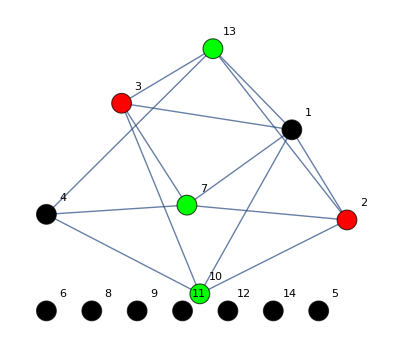

G2

NCOLORACIONES[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,1,0,1,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,1,0,1,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,1,0,1,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Negro

Vértice 5, color Negro

Vértice 6, color Negro

Vértice 7, color Rojo

Vértice 8, color Negro

Vértice 9, color Negro

Vértice 10, color Rojo

Vértice 11, color Negro

Vértice 12, color Negro

Vértice 13, color Rojo

Vértice 14, color Negro

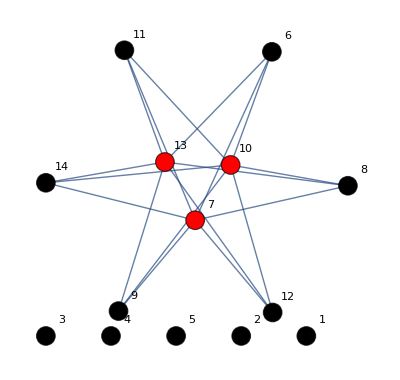

G3

NCOLORACIONES[{{0,1,1,0,0,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,1,0,0},{1,0,0,0,0,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Rojo

Vértice 6, color Rojo

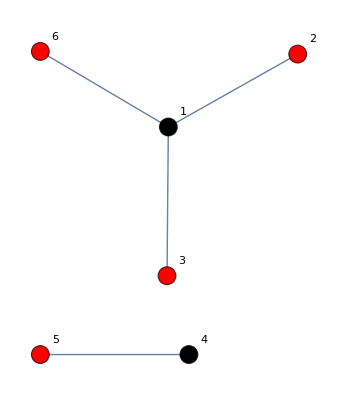

G4

NCOLORACIONES[{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

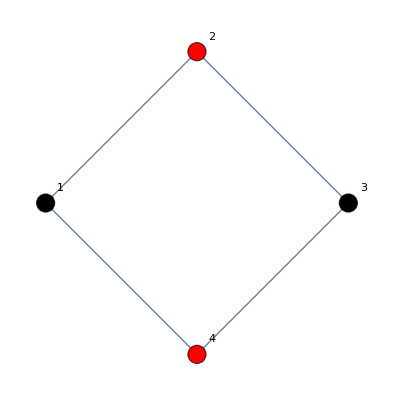

G5

NCOLORACIONES[{{0,0,0,1,1},{0,0,0,1,1},{0,0,0,1,1},{1,1,1,0,0},{1,1,1,0,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

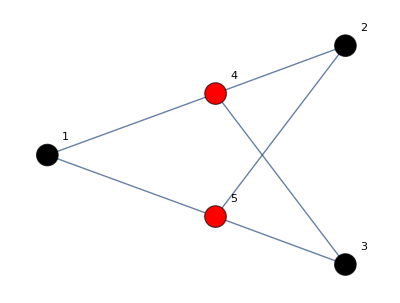

G6

NCOLORACIONES[{{0,1,0,1,0,0,0,1},{1,0,1,0,0,0,1,0},{0,1,0,1,0,1,0,0},{1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1},{0,0,1,0,1,0,1,0},{0,1,0,0,0,1,0,1},{1,0,0,0,1,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

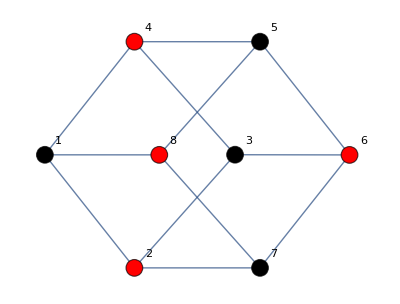

G7

NCOLORACIONES[{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}]

4

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

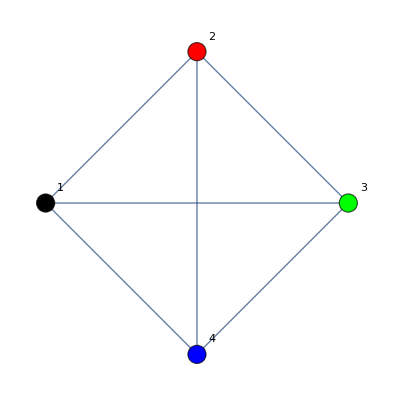

G8

NCOLORACIONES[{{0,1,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

Vértice 9, color Negro

Vértice 10, color Rojo

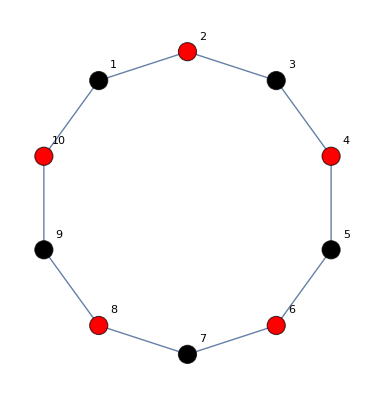

G9

NCOLORACIONES[{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

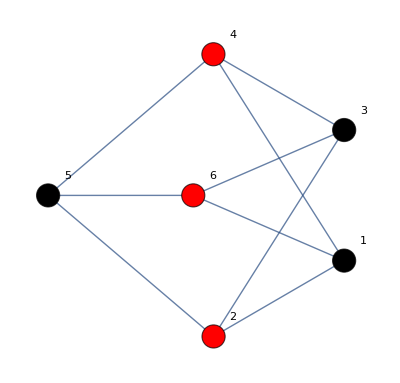

```mathematica
"Comatico y coloración optima"
"G1"
AG1=MATRIZADYACENCIA[WG1,FG1];
NCOLORACIONES[AG1]
NUMEROCROMATICO[AG1]
DIBUJAR[AG1]
"G2"
AG2=MATRIZADYACENCIA[WG2,FG2];
NCOLORACIONES[AG2]
NUMEROCROMATICO[AG2]
DIBUJAR[AG2]
"G3"
AG3=MATRIZADYACENCIA[WG3,FG3];
NCOLORACIONES[AG3]
NUMEROCROMATICO[AG3]
DIBUJAR[AG3]
"G4"
AG4=MATRIZADYACENCIA[WG4,FG4];
NCOLORACIONES[AG4]
NUMEROCROMATICO[AG4]
DIBUJAR[AG4]
"G5"
AG5=MATRIZADYACENCIA[WG5,FG5];
NCOLORACIONES[AG5]
NUMEROCROMATICO[AG5]
DIBUJAR[AG5]
"G6"
AG6=MATRIZADYACENCIA[WG6,FG6];
NCOLORACIONES[AG6]
NUMEROCROMATICO[AG6]
DIBUJAR[AG6]
"G7"
AG7=MATRIZADYACENCIA[WG7,FG7];
NCOLORACIONES[AG7]
NUMEROCROMATICO[AG7]
DIBUJAR[AG7]
"G8"
AG8=MATRIZADYACENCIA[WG8,FG8];
NCOLORACIONES[AG8]
NUMEROCROMATICO[AG8]
DIBUJAR[AG8]
"G9"
AG9=MATRIZADYACENCIA[WG9,FG9];
NCOLORACIONES[AG9]
NUMEROCROMATICO[AG9]
DIBUJAR[AG9]
```

Plano

G1

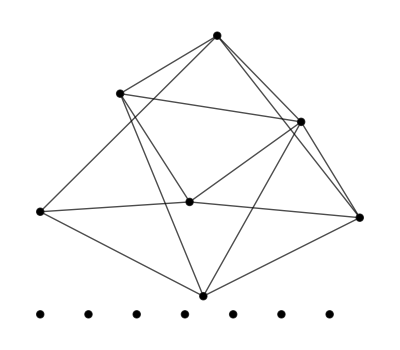

False

G2

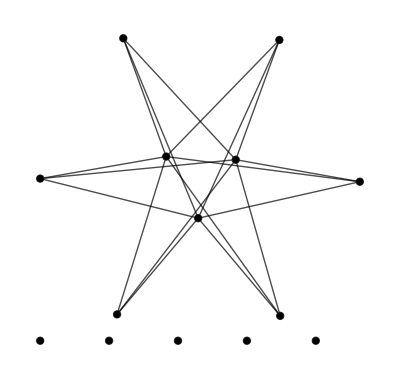

False

G3

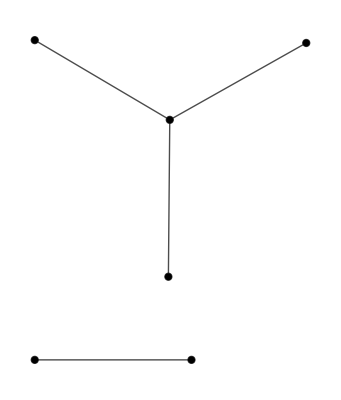

True

G4

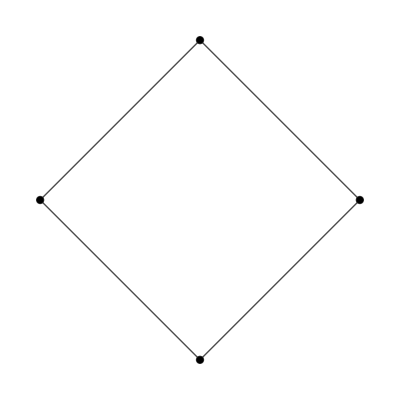

True

G5

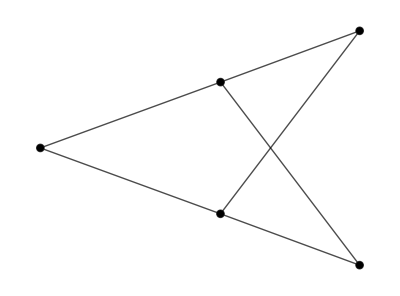

True

G6

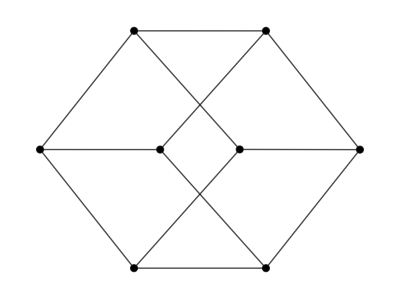

True

G7

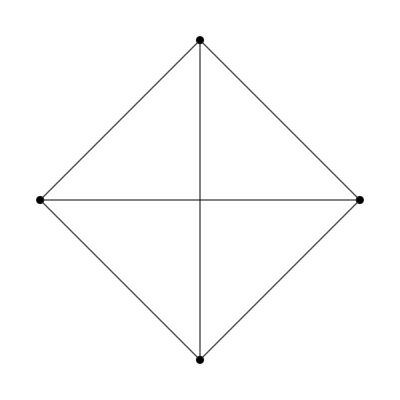

True

G1

-Graphics-

False

G8

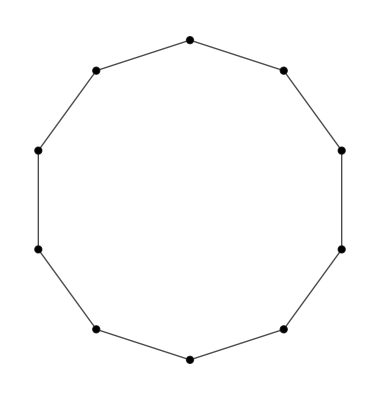

True

G9

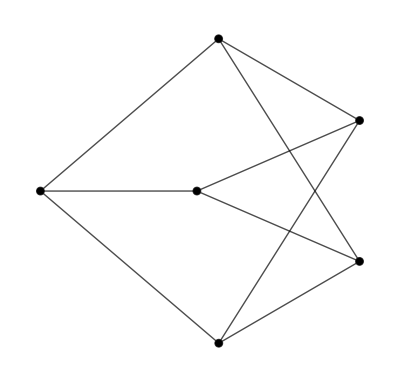

False

```mathematica
"Plano"
"G1"
GraphPlot[AG1,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG1]
"G2"
GraphPlot[AG2,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG2]
"G3"
GraphPlot[AG3,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG3]
"G4"
GraphPlot[AG4,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG4]
"G5"
GraphPlot[AG5,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG5]
"G6"
GraphPlot[AG6,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG6]
"G7"
GraphPlot[AG7,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG7]
"G1"
GraphPlot[AG1,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG1]
"G8"
GraphPlot[AG8,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG8]
"G9"
GraphPlot[AG9,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG9]
```

```mathematica
"Arbol"
"G1"
ARBOL[AG1]
"G2"
ARBOL[AG2]
"G3"
ARBOL[AG3]
"G4"
ARBOL[AG4]
"G5"
ARBOL[AG5]
"G6"
ARBOL[AG6]
"G7"
ARBOL[AG7]
"G8"
ARBOL[AG8]
"G9"
ARBOL[AG9]
```

Arbol

G1

False

G2

False

G3

False

G4

False

G5

False

G6

False

G7

False

G8

False

G9

False

#### b) Cada uno de los grafos del ejercicio 6.8 del manual de prácticas

```mathematica
"Eje68 G1"
NCOLORACIONES[Eje68G1Adya]
NUMEROCROMATICO[Eje68G1Adya]
"Plano"
PLANO[Eje68G1Adya]
"Arbol"
ARBOL[Eje68G1Adya]
DIBUJAR[Eje68G1Adya]
"Eje68 G2"
NCOLORACIONES[Eje68G2Adya]
NUMEROCROMATICO[Eje68G2Adya]
"Plano"
PLANO[Eje68G2Adya]
"Arbol"
ARBOL[Eje68G2Adya]
DIBUJAR[Eje68G2Adya]
"Eje68 G3"
NCOLORACIONES[Eje68G3Adya]
NUMEROCROMATICO[Eje68G3Adya]
"Plano"
PLANO[Eje68G3Adya]
"Arbol"
ARBOL[Eje68G3Adya]
DIBUJAR[Eje68G3Adya]
"Eje68 G4"
NCOLORACIONES[Eje68G4Adya]
NUMEROCROMATICO[Eje68G4Adya]
"Plano"
PLANO[Eje68G4Adya]
"Arbol"
ARBOL[Eje68G4Adya]
DIBUJAR[Eje68G4Adya]
"Eje68 G5"
NCOLORACIONES[Eje68G5Adya]
NUMEROCROMATICO[Eje68G5Adya]
"Plano"
PLANO[Eje68G5Adya]
"Arbol"
ARBOL[Eje68G5Adya]
DIBUJAR[Eje68G5Adya]
```

Eje68 G1

NCOLORACIONES[{{0,1,1,0,0,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,1,0,0},{1,0,0,0,0,0}}]

2

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Rojo

Vértice 6, color Rojo

-Graphics-

Eje68 G2

NCOLORACIONES[{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}]

2

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

-Graphics-

Eje68 G3

NCOLORACIONES[{{0,0,0,1,1},{0,0,0,1,1},{0,0,0,1,1},{1,1,1,0,0},{1,1,1,0,0}}]

2

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

-Graphics-

Eje68 G4

NCOLORACIONES[{{0,1,0,1,0,0,0,1},{1,0,1,0,0,0,1,0},{0,1,0,1,0,1,0,0},{1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1},{0,0,1,0,1,0,1,0},{0,1,0,0,0,1,0,1},{1,0,0,0,1,0,1,0}}]

2

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

-Graphics-

Eje68 G5

NCOLORACIONES[{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}]

4

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

-Graphics-

#### c) Un octógono

Octogono

NCOLORACIONES[{{0,1,0,0,0,0,0,1},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,0},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{1,0,0,0,0,0,1,0}}]

2

Plano

True

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

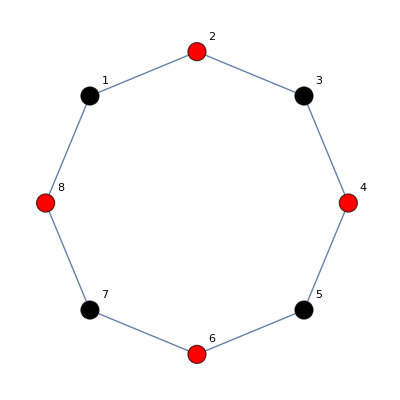

```mathematica
"Octogono"
NCOLORACIONES[octoAdya]
NUMEROCROMATICO[octoAdya]
"Plano"
PLANO[octoAdya]
"Arbol"
ARBOL[octoAdya]
DIBUJAR[octoAdya]
```

#### d) K7

K7

NCOLORACIONES[{{0,1,1,1,1,1,1},{1,0,1,1,1,1,1},{1,1,0,1,1,1,1},{1,1,1,0,1,1,1},{1,1,1,1,0,1,1},{1,1,1,1,1,0,1},{1,1,1,1,1,1,0}}]

7

Plano

False

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

Vértice 5, color Amarillo

Vértice 6, color Cyan

Vértice 7, color Marrón

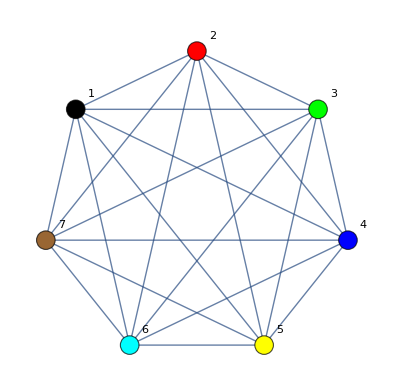

```mathematica
k7Adya=({{0, 1, 1, 1, 1, 1, 1}, {1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1, 1}, {1, 1, 1, 0, 1, 1, 1}, {1, 1, 1, 1, 0, 1, 1}, {1, 1, 1, 1, 1, 0, 1}, {1, 1, 1, 1, 1, 1, 0}});
"K7"
NCOLORACIONES[k7Adya]
NUMEROCROMATICO[k7Adya]
"Plano"
PLANO[k7Adya]
"Arbol"
ARBOL[k7Adya]
DIBUJAR[k7Adya]
```

#### e) K4,3

k43

NCOLORACIONES[{{0,0,0,0,1,1,1},{0,0,0,0,1,1,1},{0,0,0,0,1,1,1},{0,0,0,0,1,1,1},{1,1,1,1,0,0,0},{1,1,1,1,0,0,0},{1,1,1,1,0,0,0}}]

2

Plano

False

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Negro

Vértice 5, color Rojo

Vértice 6, color Rojo

Vértice 7, color Rojo

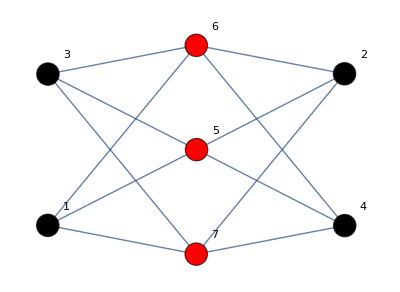

```mathematica
"k43"
NCOLORACIONES[k43Adya]
NUMEROCROMATICO[k43Adya]
"Plano"
PLANO[k43Adya]
"Arbol"
ARBOL[k43Adya]
DIBUJAR[k43Adya]
```

#### f) Grafo del ejercicio 3 de la convocatoria ordinaria 2 del curso 2023/24

```mathematica
"Ejer 3 Ord2 22/23"
NCOLORACIONES[Eje3Ord22324Adya]
NUMEROCROMATICO[Eje3Ord22324Adya]
"Plano"
PLANO[Eje3Ord22324Adya]
"Arbol"
ARBOL[Eje3Ord22324Adya]
DIBUJAR[Eje3Ord22324Adya]
```

Ejer 3 Ord2 22/23

NCOLORACIONES[{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}}]

2

Plano

False

Arbol

False

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

-Graphics-